```mathematica
(* Dawid Bitner *)
(* projekt 5 *)
symulacja[ec_]:=Module[{},
(* rozwiązujemy równanie różniczkowe, aby uzyskać wartość prędkości komety w chwili t *)
sol=NDSolve[{v'[s]*(1+ec)^2/(1+Cos[v[s]]*ec)^2==1,v[0]==0},v[s],{s,-1000,1000}]⟦1,1,2⟧;
v[t_]:=sol/.s->t;

(* wyznaczamy położenie komety w chwili t *)
x[t_]:=(1+ec)Cos[v[t]]/(1+ec*Cos[v[t]]);
y[t_]:=(1+ec)Sin[v[t]]/(1+ec*Cos[v[t]]);

(* zaznaczamy trajektorię ruchu komety na wykresie oraz dodajemy Słońce w punkcie początku układu współrzędnych *)
tr=ParametricPlot[{x[t],y[t]},{t,-1000,1000}, AspectRatio->Automatic, PlotStyle->{Gray,Dashed}];
sun = Graphics[{Yellow, Disk[{0,0},0.5]}];
Print[Show[tr,sun, PlotLabel->"trajektoria ruchu komety wokół słońca", PlotRange->{{-10,1.5}, {-10,10}}]];
]
```

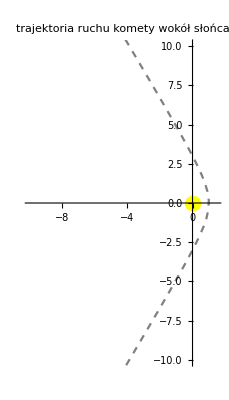

```mathematica
(* ec = 2.0 *)
symulacja[2]
```